### Find the eigenvalues of the tight-binding model in k-space

```mathematica
H=-({{0, Exp[-I ky]+Exp[-I(-Sqrt[3] kx/2-ky/2)]+Exp[-I(Sqrt[3] kx/2-ky/2)]}, {Exp[I ky]+Exp[I(-Sqrt[3] kx/2-ky/2)]+Exp[I(Sqrt[3] kx/2-ky/2)], 0}});
```

```mathematica
FullSimplify[Eigenvalues[H]]
```

{-ⅇ^(-1/4 ⅈ (2 √3 kx+3 ky)) √(ⅇ^(1/2 ⅈ (2 √3 kx+3 ky)) (3+2 Cos[√3 kx]+4 Cos[(√3 kx)/2] Cos[(3 ky)/2])),ⅇ^(-1/4 ⅈ (2 √3 kx+3 ky)) √(ⅇ^(1/2 ⅈ (2 √3 kx+3 ky)) (3+2 Cos[√3 kx]+4 Cos[(√3 kx)/2] Cos[(3 ky)/2]))}

### Define the dispersion relation function

```mathematica
F[kx_,ky_]:={- 3√ (3+2 Cos[√3 kx]+4 Cos[(√3 kx)/2] Cos[(3 ky)/2]),3√ (3+2 Cos[√3 kx]+4 Cos[(√3 kx)/2] Cos[(3 ky)/2])}
```

### 3D Plot

```mathematica
Plot3D[F[x,y],{x,-4Pi/3/Sqrt[3],4Pi/3/Sqrt[3]},{y,-2Pi/3,2Pi/3},RegionFunction->Function[{x,y,z},Abs[x+y/Sqrt[3]]≤4Pi/3/Sqrt[3]&&Abs[x-y/Sqrt[3]]≤4Pi/3/Sqrt[3]],AxesLabel->{kx,ky,Energy}]
```

-Graphics3D-

### 2D Countour Plot (The lower band)

```mathematica
F[x,y][[1]]
```

-3 √(3+2 Cos[√3 x]+4 Cos[(√3 x)/2] Cos[(3 y)/2])

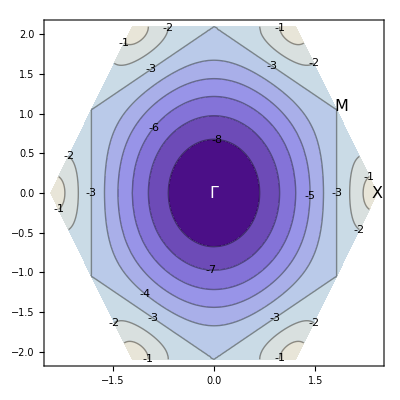

```mathematica
ContourPlot[F[x+0.0,y+0.0][[1]],{x,-4Pi/3/Sqrt[3],4Pi/3/Sqrt[3]},{y,-2Pi/3,2Pi/3},RegionFunction->Function[{x,y,z},Abs[x+y/Sqrt[3]]≤4Pi/3/Sqrt[3]&&Abs[x-y/Sqrt[3]]≤4Pi/3/Sqrt[3]],Epilog->{White,Text[Style[Γ,16],{0,0}],Black,Text[Style[M,16],{(Pi+0.12)/Sqrt[3],(Pi+0.12)/3}],Black,Text[Style[X,16],{4Pi/3/Sqrt[3],0}]},ContourLabels->All]
```

### 1D plot along

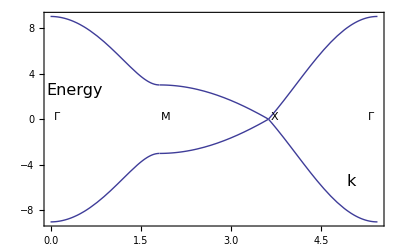

```mathematica
Plot[Piecewise[{{F[t,t/Sqrt[3]],t≥0&&t<Pi/Sqrt[3]},{F[(t-Pi/Sqrt[3])/3+Pi/Sqrt[3],(2Pi/3-t/Sqrt[3])],t≥Pi/Sqrt[3]&&t<2Pi/Sqrt[3]},{F[4/3(Pi/Sqrt[3]-(t-2Pi/Sqrt[3])),0],t≥2Pi/Sqrt[3]&&t<3Pi/Sqrt[3]}}],{t,0,Sqrt[3]Pi},GridLines->{{{Pi/Sqrt[3],Dashed},{2Pi/Sqrt[3],Dashed},{0,Dashed},{3Pi/Sqrt[3],Dashed}},{}},Epilog->{Inset["Γ",{0.1,0.2}],Inset["M",{Pi/Sqrt[3]+0.1,0.2}],Inset["X",{2Pi/Sqrt[3]+0.1,0.2}],Inset["Γ",{3Pi/Sqrt[3]-0.1,0.2}],Inset[Style["k",16],{5,-5.5}],Inset[Style["Energy",16],{0.4,2.5}]},Frame->True]
```

```mathematica
Array[EN,400];
```

```mathematica
nn=1;While[nn<401,EN[nn]=0;nn++];
```

```mathematica
For[i=0,i≤200,i++,
For[j=0,j≤200,j++,
{
energy=F[i Pi/Sqrt[3]/100-Pi/Sqrt[3],2j Pi/3/100-2Pi/3]//N;    (* make sure energy is represented in the form 1.234 and not Cos[...] *)
n=Rescale[energy[[1]],{-9,9},{1,400}]//Round;    (* find appropriate bin for band 1*)
EN[n]++;
n=Rescale[energy[[2]],{-9,9},{1,400}]//Round;    (* find appropriate bin for band 2*)
EN[n]++
}
]
]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

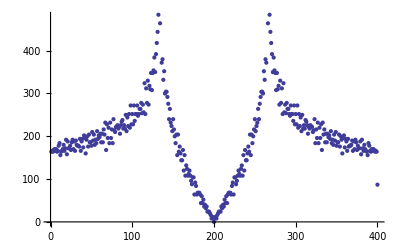

```mathematica
ListPlot[Table[{i,EN[i]},{i,1,400}]]
```

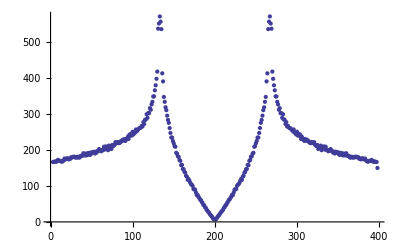

```mathematica
ListPlot[Table[{i,(EN[i-1]+EN[i-2]+EN[i]+EN[i+1]+EN[i+2])/5},{i,3,398}]]
```